```mathematica
dataRaw=Import["C:\\Users\\juhaszn\\Documents\\HAL\\stochasticVariability\\output\\2022-04-27_09-53-58\\dataLastTick.csv"]
```

{{0.},{1.},{18.},{31.},{6.}}

```mathematica
data=Flatten[dataRaw]
```

{0.,1.,18.,31.,6.}

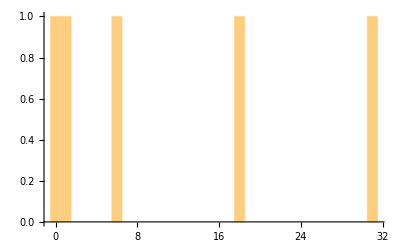

```mathematica
Histogram[data,Round[Max[data]]]
```

```mathematica
histogramList=HistogramList[data,Round[Max[data]]][[2]]
```

{1,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
probabilities=histogramList/Length[data]
```

{1/5,1/5,0,0,0,0,1/5,0,0,0,0,0,0,0,0,0,0,0,1/5,0,0,0,0,0,0,0,0,0,0,0,0,1/5}

```mathematica
G[z_]:=Module[{},
sum=0;
For[i=1,i<=Length[histogramList],i++,
sum=sum+(Power[z,i-1])*probabilities[[i]]];
sum]
G[1.0]
```

1.

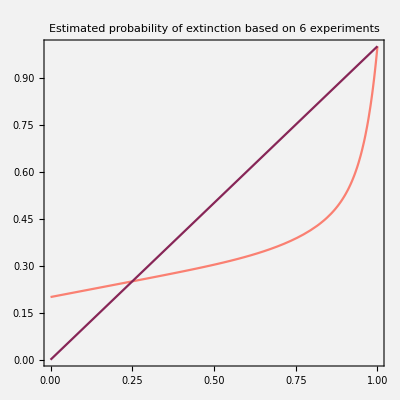

```mathematica
Plot[{G[z],z},{z,0,1},
AspectRatio->1,PlotRange->All,
PlotStyle->{ColorData["Legacy","Salmon"],ColorData["Legacy","Raspberry"]},
Frame->True,
PlotLabel->Style["Estimated probability of extinction based on 6 experiments",FontSize->12],
FrameStyle->Directive[ColorData["Legacy","SeaGreen"]],
Background->Lighter[Gray, 0.9]]
```